## Fig3

```mathematica
ρNR[a_]:=300 a^-3
ρr[a_]:=1000 a^-4
ρΛ[a_]:=1
```

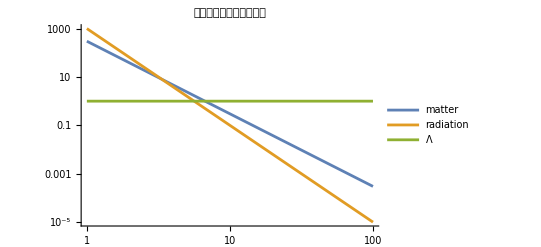

```mathematica
LogLogPlot[{ρNR[a],ρr[a],ρΛ[a]},{a,1,100},PlotLegends->{"matter","radiation","Λ"},PlotLabel->"不同物质的能量密度变化"]
```

```mathematica
Ωmatter[a_]:=ρNR[a]/(ρNR[a]+ρr[a]+ρΛ[a])
Ωr[a_]:=ρr[a]/(ρNR[a]+ρr[a]+ρΛ[a])
ΩΛ[a_]:=ρΛ[a]/(ρNR[a]+ρr[a]+ρΛ[a])
```

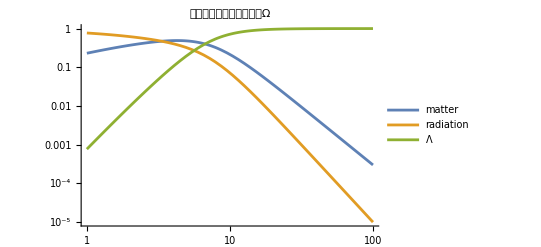

```mathematica
LogLogPlot[{Ωmatter[a],Ωr[a],ΩΛ[a]},{a,1,100},PlotLegends->{"matter","radiation","Λ"},PlotLabel->"不同物质的能量密度分数Ω"]
```